```mathematica
R:=8.31
T:=293
M:=28.97/1000
g:=9.8
h:=-10
```

```mathematica
solution=NDSolve[{y''[t]==-g-(R*T)/(M*y[t]),y[0]==h,y'[0]==0},y,{t,0,10}]
```

NDSolve::ndsz: At t == 0.0432523, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

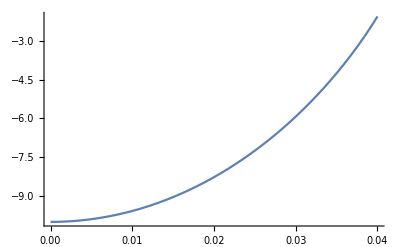

```mathematica
Plot[Evaluate[y[t]/. solution],{t,0,0.04}]
```

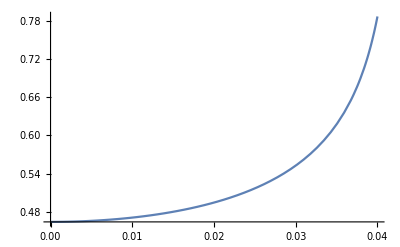

```mathematica
Plot[Evaluate[CubeRoot[-1/(y[t]/. solution)]],{t,0,0.04}]
```

```mathematica
Manipulate[Graphics[{Circle[{0,(y[t]/.solution)[[1]]},CubeRoot[-1/(y[t]/. solution)][[1]]]},PlotRange->{{-1,1},{-11,0}}],{t,0,0.04}]
```